# All 605 of them

## This is NOT a standalone notebook

## Normal Form

```mathematica
Clear[α,β,a1,a2,a3,yHat2,yHat1,yHat0,yHat]
Clear[γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

yHat2List={(*1*)0.2,(*2*)0.63,(*3*)1.05,(*4*)1.14,(*5*)1.62,(*6*)2.25,(*7*)2.73,(*8*)3.39,(*9*)3.93,(*10*)4.38,(*11*)4.80};
yHat1List={(*1*)0.69,(*2*)0.99,(*3*)1.65,(*4*)1.95,(*5*)2.13,(*6*)2.55,(*7*)3.06,(*8*)3.12,(*9*)3.42,(*10*)4.23,(*11*)4.35};
yHat0List={(*1*)0.87,(*2*)1.89,(*3*)2.97,(*4*)4.17,(*5*)4.26};


plotplotlist={};
For[z=1,z<=Length[yHat1List],z++,
For[x=1,x<=Length[yHat0List],x++,
For[m=1,m<=Length[yHat2List],m++,
yHat2=yHat2List[[m]];
yHat1=yHat1List[[z]];
yHat0=yHat0List[[x]];

γ22=γ22/.{bdCoeffs2[[3]]/.interiorCoeffs};
γ20=1/γ22*(γ20/.{bdCoeffs2[[1]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
γ21=1/γ22*(γ21/.{bdCoeffs2[[2]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
γ23=1/γ22*(γ23/.{bdCoeffs2[[4]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
γ24=1/γ22*(γ24/.{bdCoeffs2[[5]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
a20=1/γ22*(a20/.{bdCoeffs2[[6]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
a21=1/γ22*(a21/.{bdCoeffs2[[7]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
a22=1/γ22*(a22/.{bdCoeffs2[[8]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
a23=1/γ22*(a23/.{bdCoeffs2[[9]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
a24=1/γ22*(a24/.{bdCoeffs2[[10]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
a25=1/γ22*(a25/.{bdCoeffs2[[11]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
a26=1/γ22*(a26/.{bdCoeffs2[[12]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
γ22=γ22/γ22/.{yHat->yHat2};



γ11=γ11/.{bdCoeffs1[[2]]/.interiorCoeffs};
γ10=1/γ11*(γ10/.{bdCoeffs1[[1]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
γ12=1/γ11*(γ12/.{bdCoeffs1[[3]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
γ13=1/γ11*(γ13/.{bdCoeffs1[[4]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
a10=1/γ11*(a10/.{bdCoeffs1[[5]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
a11=1/γ11*(a11/.{bdCoeffs1[[6]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
a12=1/γ11*(a12/.{bdCoeffs1[[7]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
a13=1/γ11*(a13/.{bdCoeffs1[[8]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
a14=1/γ11*(a14/.{bdCoeffs1[[9]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
a15=1/γ11*(a15/.{bdCoeffs1[[10]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
a16=1/γ11*(a16/.{bdCoeffs1[[11]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
γ11=γ11/γ11/.{yHat->yHat1};



γ00=γ00/.{bdCoeffs0[[1]]/.interiorCoeffs};
γ01=1/γ00*(γ01/.{bdCoeffs0[[2]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
γ02=1/γ00*(γ02/.{bdCoeffs0[[3]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
a00=1/γ00*(a00/.{bdCoeffs0[[4]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
a01=1/γ00*(a01/.{bdCoeffs0[[5]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
a02=1/γ00*(a02/.{bdCoeffs0[[6]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
a03=1/γ00*(a03/.{bdCoeffs0[[7]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
a04=1/γ00*(a04/.{bdCoeffs0[[8]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
a05=1/γ00*(a05/.{bdCoeffs0[[9]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
a06=1/γ00*(a06/.{bdCoeffs0[[10]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
γ00=γ00/γ00/.{yHat->yHat0};

interior={α->0.5770460201292381,β->0.08900836845092142,a->0.6517078440898839,b->0.24815882627035918,c->0.006009630649852392};
boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};
coeff=Flatten[Join[interior,boundary]];

LHSBorders={
{1,α12,β12},
{α21,1,α22,β22},
{β31,α31,1,α32,β32}
};
RHSBorders={
{a1,b1,c1,d1,e1,f1,g1},
{a2,b2,c2,d2,e2,f2,g2},
{a3,b3,c3,d3,e3,f3,g3}
};

LHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[LHSBorders[[i]]],j++,
M[[i,j]]=LHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=LHSBorders[[i,j]]/.coeff
]
];

M
];

RHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a,
Band[{3,1}]->-b,
Band[{4,1}]->-c,
Band[{1,2}]->a,
Band[{1,3}]->b,
Band[{1,4}]->c
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
];

n=160;
LHS=LHSMatrix[n,3,coeff];
RHS=RHSMatrix[n,3,coeff];

For[j=1,j<=n,j++,LHS[[1,j]]=0];
For[j=1,j<=n,j++,LHS[[j,1]]=0];
For[j=1,j<=n,j++,RHS[[1,j]]=0];
For[j=1,j<=n,j++,RHS[[j,1]]=0];
LHS[[1,1]]=1;
LHS//MatrixForm;
RHS//MatrixForm;

mat=Inverse[LHS].RHS;
eigs=Eigenvalues[mat];
AppendTo[plotplotlist,ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[160]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]]]
]
]
];
```

## Table and Color Form

```mathematica
Clear[α,β,a1,a2,a3,yHat2,yHat1,yHat0,yHat]
Clear[γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

yHat2List={(*1*)0.2,(*2*)0.63,(*3*)1.05,(*4*)1.14,(*5*)1.62,(*6*)2.25,(*7*)2.73,(*8*)3.39,(*9*)3.93,(*10*)4.38,(*11*)4.80};
yHat1List={(*1*)0.69,(*2*)0.99,(*3*)1.65,(*4*)1.95,(*5*)2.13,(*6*)2.55,(*7*)3.06,(*8*)3.12,(*9*)3.42,(*10*)4.23,(*11*)4.35};
yHat0List={(*1*)0.87,(*2*)1.89,(*3*)2.97,(*4*)4.17,(*5*)4.26};

plotplotlist=ParallelTable[
γ22=γ22/.{bdCoeffs2[[3]]/.interiorCoeffs};
γ20=1/γ22*(γ20/.{bdCoeffs2[[1]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ21=1/γ22*(γ21/.{bdCoeffs2[[2]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ23=1/γ22*(γ23/.{bdCoeffs2[[4]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ24=1/γ22*(γ24/.{bdCoeffs2[[5]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a20=1/γ22*(a20/.{bdCoeffs2[[6]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a21=1/γ22*(a21/.{bdCoeffs2[[7]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a22=1/γ22*(a22/.{bdCoeffs2[[8]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a23=1/γ22*(a23/.{bdCoeffs2[[9]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a24=1/γ22*(a24/.{bdCoeffs2[[10]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a25=1/γ22*(a25/.{bdCoeffs2[[11]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a26=1/γ22*(a26/.{bdCoeffs2[[12]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ22=γ22/γ22/.{yHat->yHat2List[[xx]]};



γ11=γ11/.{bdCoeffs1[[2]]/.interiorCoeffs};
γ10=1/γ11*(γ10/.{bdCoeffs1[[1]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
γ12=1/γ11*(γ12/.{bdCoeffs1[[3]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
γ13=1/γ11*(γ13/.{bdCoeffs1[[4]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a10=1/γ11*(a10/.{bdCoeffs1[[5]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a11=1/γ11*(a11/.{bdCoeffs1[[6]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a12=1/γ11*(a12/.{bdCoeffs1[[7]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a13=1/γ11*(a13/.{bdCoeffs1[[8]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a14=1/γ11*(a14/.{bdCoeffs1[[9]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a15=1/γ11*(a15/.{bdCoeffs1[[10]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a16=1/γ11*(a16/.{bdCoeffs1[[11]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
γ11=γ11/γ11/.{yHat->yHat1List[[yy]]};



γ00=γ00/.{bdCoeffs0[[1]]/.interiorCoeffs};
γ01=1/γ00*(γ01/.{bdCoeffs0[[2]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
γ02=1/γ00*(γ02/.{bdCoeffs0[[3]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a00=1/γ00*(a00/.{bdCoeffs0[[4]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a01=1/γ00*(a01/.{bdCoeffs0[[5]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a02=1/γ00*(a02/.{bdCoeffs0[[6]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a03=1/γ00*(a03/.{bdCoeffs0[[7]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a04=1/γ00*(a04/.{bdCoeffs0[[8]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a05=1/γ00*(a05/.{bdCoeffs0[[9]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a06=1/γ00*(a06/.{bdCoeffs0[[10]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
γ00=γ00/γ00/.{yHat->yHat0List[[zz]]};

interior={α->0.5770460201292381,β->0.08900836845092142,a->0.6517078440898839,b->0.24815882627035918,c->0.006009630649852392};
boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};
coeff=Flatten[Join[interior,boundary]];

LHSBorders={
{1,α12,β12},
{α21,1,α22,β22},
{β31,α31,1,α32,β32}
};
RHSBorders={
{a1,b1,c1,d1,e1,f1,g1},
{a2,b2,c2,d2,e2,f2,g2},
{a3,b3,c3,d3,e3,f3,g3}
};

LHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[LHSBorders[[i]]],j++,
M[[i,j]]=LHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=LHSBorders[[i,j]]/.coeff
]
];

M
];

RHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a,
Band[{3,1}]->-b,
Band[{4,1}]->-c,
Band[{1,2}]->a,
Band[{1,3}]->b,
Band[{1,4}]->c
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
];

n=160;
LHS=LHSMatrix[n,3,coeff];
RHS=RHSMatrix[n,3,coeff];

For[j=1,j<=n,j++,LHS[[1,j]]=0];
For[j=1,j<=n,j++,LHS[[j,1]]=0];
For[j=1,j<=n,j++,RHS[[1,j]]=0];
For[j=1,j<=n,j++,RHS[[j,1]]=0];
LHS[[1,1]]=1;
LHS//MatrixForm;
RHS//MatrixForm;

mat=Inverse[LHS].RHS;
eigs=-Eigenvalues[mat];
ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[160]," and\n","(ŷ)_0 = ",ToString[yHat0List[[zz]]],", (ŷ)_1 = ",ToString[yHat1List[[yy]]],", (ŷ)_2 = ",ToString[yHat2List[[xx]]]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0List[[zz]]/5,yHat1List[[yy]]/5,yHat2List[[xx]]/5]],
{xx,1,3},{yy,1,3},{zz,1,3}];
```

## Output

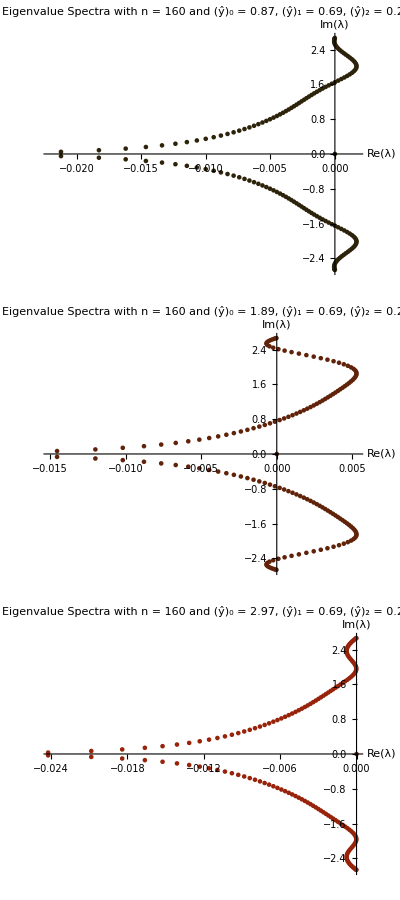
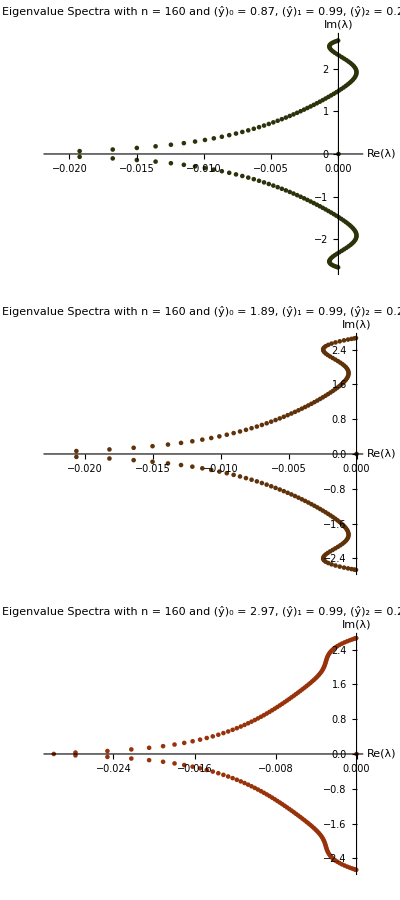
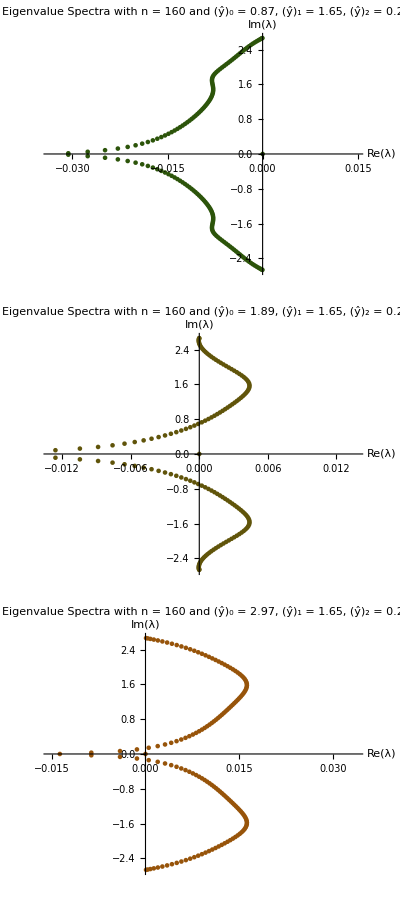
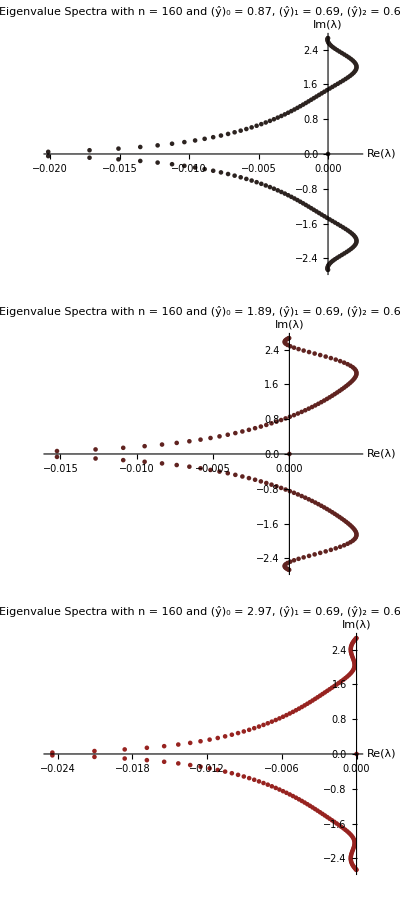
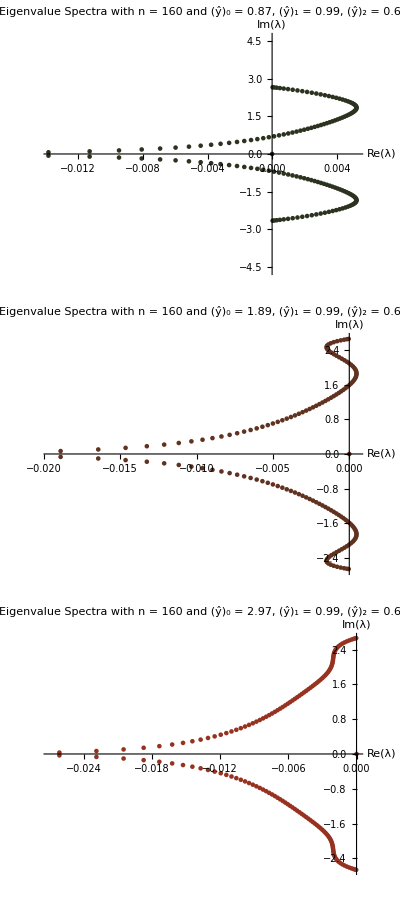
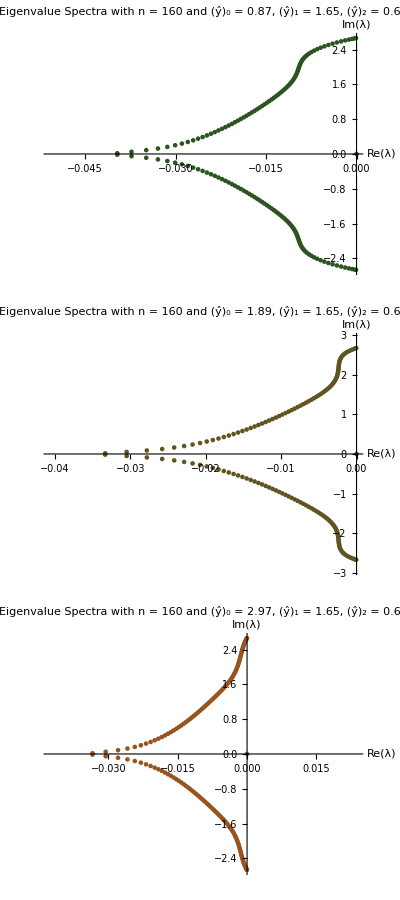
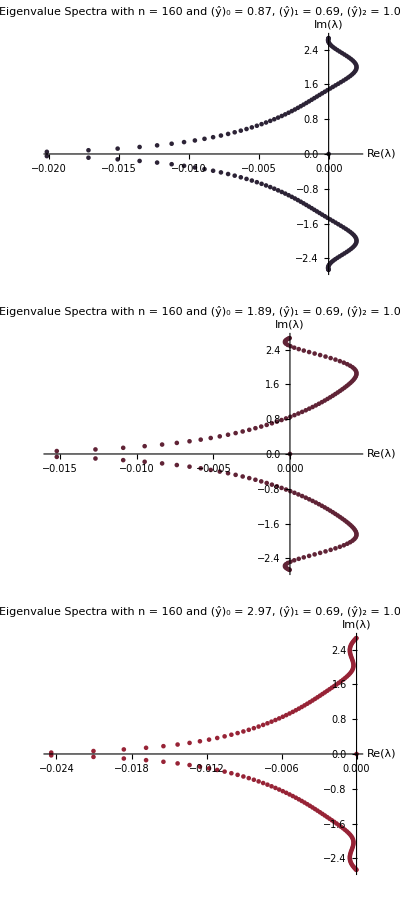
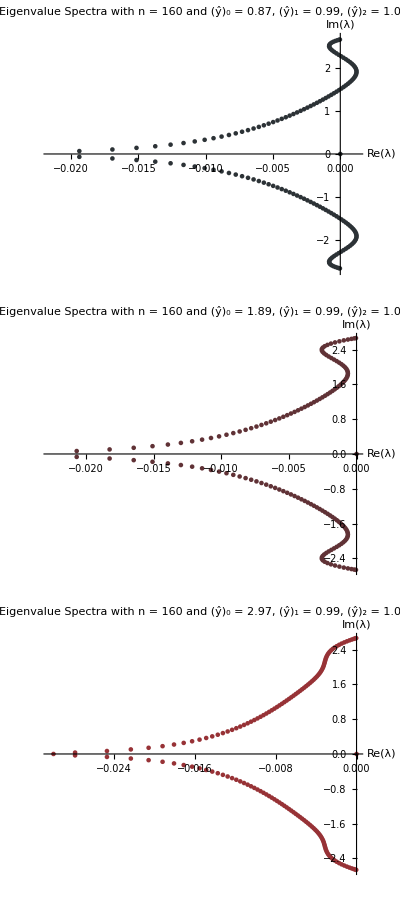
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
plotplotlist//TableForm
```

## Max(Re)

```mathematica
Clear[α,β,a1,a2,a3,yHat2,yHat1,yHat0,yHat]
Clear[γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

yHat2List={(*1*)0.2,(*2*)0.63,(*3*)1.05,(*4*)1.14,(*5*)1.62,(*6*)2.25,(*7*)2.73,(*8*)3.39,(*9*)3.93,(*10*)4.38,(*11*)4.80};
yHat1List={(*1*)0.69,(*2*)0.99,(*3*)1.65,(*4*)1.95,(*5*)2.13,(*6*)2.55,(*7*)3.06,(*8*)3.12,(*9*)3.42,(*10*)4.23,(*11*)4.35};
yHat0List={(*1*)0.87,(*2*)1.89,(*3*)2.97,(*4*)4.17,(*5*)4.26};

maxrelist=ParallelTable[
γ22=γ22/.{bdCoeffs2[[3]]/.interiorCoeffs};
γ20=1/γ22*(γ20/.{bdCoeffs2[[1]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ21=1/γ22*(γ21/.{bdCoeffs2[[2]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ23=1/γ22*(γ23/.{bdCoeffs2[[4]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ24=1/γ22*(γ24/.{bdCoeffs2[[5]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a20=1/γ22*(a20/.{bdCoeffs2[[6]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a21=1/γ22*(a21/.{bdCoeffs2[[7]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a22=1/γ22*(a22/.{bdCoeffs2[[8]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a23=1/γ22*(a23/.{bdCoeffs2[[9]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a24=1/γ22*(a24/.{bdCoeffs2[[10]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a25=1/γ22*(a25/.{bdCoeffs2[[11]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a26=1/γ22*(a26/.{bdCoeffs2[[12]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ22=γ22/γ22/.{yHat->yHat2List[[xx]]};



γ11=γ11/.{bdCoeffs1[[2]]/.interiorCoeffs};
γ10=1/γ11*(γ10/.{bdCoeffs1[[1]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
γ12=1/γ11*(γ12/.{bdCoeffs1[[3]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
γ13=1/γ11*(γ13/.{bdCoeffs1[[4]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a10=1/γ11*(a10/.{bdCoeffs1[[5]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a11=1/γ11*(a11/.{bdCoeffs1[[6]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a12=1/γ11*(a12/.{bdCoeffs1[[7]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a13=1/γ11*(a13/.{bdCoeffs1[[8]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a14=1/γ11*(a14/.{bdCoeffs1[[9]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a15=1/γ11*(a15/.{bdCoeffs1[[10]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a16=1/γ11*(a16/.{bdCoeffs1[[11]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
γ11=γ11/γ11/.{yHat->yHat1List[[yy]]};



γ00=γ00/.{bdCoeffs0[[1]]/.interiorCoeffs};
γ01=1/γ00*(γ01/.{bdCoeffs0[[2]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
γ02=1/γ00*(γ02/.{bdCoeffs0[[3]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a00=1/γ00*(a00/.{bdCoeffs0[[4]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a01=1/γ00*(a01/.{bdCoeffs0[[5]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a02=1/γ00*(a02/.{bdCoeffs0[[6]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a03=1/γ00*(a03/.{bdCoeffs0[[7]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a04=1/γ00*(a04/.{bdCoeffs0[[8]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a05=1/γ00*(a05/.{bdCoeffs0[[9]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a06=1/γ00*(a06/.{bdCoeffs0[[10]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
γ00=γ00/γ00/.{yHat->yHat0List[[zz]]};

interior={α->0.5770460201292381,β->0.08900836845092142,a->0.6517078440898839,b->0.24815882627035918,c->0.006009630649852392};
boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};
coeff=Flatten[Join[interior,boundary]];

LHSBorders={
{1,α12,β12},
{α21,1,α22,β22},
{β31,α31,1,α32,β32}
};
RHSBorders={
{a1,b1,c1,d1,e1,f1,g1},
{a2,b2,c2,d2,e2,f2,g2},
{a3,b3,c3,d3,e3,f3,g3}
};

LHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[LHSBorders[[i]]],j++,
M[[i,j]]=LHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=LHSBorders[[i,j]]/.coeff
]
];

M
];

RHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a,
Band[{3,1}]->-b,
Band[{4,1}]->-c,
Band[{1,2}]->a,
Band[{1,3}]->b,
Band[{1,4}]->c
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
];

n=160;
LHS=LHSMatrix[n,3,coeff];
RHS=RHSMatrix[n,3,coeff];

For[j=1,j<=n,j++,LHS[[1,j]]=0];
For[j=1,j<=n,j++,LHS[[j,1]]=0];
For[j=1,j<=n,j++,RHS[[1,j]]=0];
For[j=1,j<=n,j++,RHS[[j,1]]=0];
LHS[[1,1]]=1;
LHS//MatrixForm;
RHS//MatrixForm;

mat=Inverse[LHS].RHS;
eigs=-Eigenvalues[mat];
{{yHat0List[[zz]],yHat1List[[yy]],yHat2List[[xx]]},Max[Re[eigs]]},
{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}];
```

```mathematica
maxrelist//TableForm;
Dimensions@maxrelist
trimmed=Flatten[maxrelist,2];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]<=0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

{11,11,5,2}

{{{2.97,0.69,0.2},0.},{{1.89,0.99,0.2},0.},{{2.97,0.99,0.2},0.},{{2.97,2.13,0.2},0.},{{0.87,2.55,0.2},0.},{{1.89,2.55,0.2},0.},{{2.97,2.55,0.2},0.},{{2.97,0.69,0.63},0.},{{2.97,0.99,0.63},0.},{{0.87,1.65,0.63},0.},{{1.89,1.65,0.63},0.},{{2.97,2.13,0.63},0.},{{2.97,2.55,0.63},0.},{{2.97,0.69,1.05},0.},{{1.89,0.99,1.05},0.},{{2.97,0.99,1.05},0.},{{0.87,3.42,1.05},0.},{{1.89,3.42,1.05},0.},{{2.97,3.42,1.05},0.},{{4.17,3.42,1.05},0.},{{2.97,0.69,1.14},0.},{{1.89,0.99,1.14},0.},{{2.97,0.99,1.14},0.},{{0.87,0.69,1.62},0.},{{0.87,0.99,1.62},0.},{{0.87,1.95,1.62},0.},{{0.87,3.42,1.62},0.},{{2.97,0.69,2.25},0.},{{1.89,0.99,2.25},0.},{{2.97,0.99,2.25},0.},{{1.89,3.42,2.25},0.},{{2.97,3.42,2.25},0.},{{2.97,4.35,2.25},0.},{{0.87,0.69,2.73},0.},{{0.87,0.99,2.73},0.},{{1.89,0.99,2.73},0.},{{2.97,0.99,2.73},0.},{{4.17,0.99,2.73},0.},{{0.87,1.65,2.73},0.},{{0.87,2.13,2.73},0.},{{1.89,2.13,2.73},0.},{{2.97,2.13,2.73},0.},{{4.17,2.13,2.73},0.},{{0.87,2.55,2.73},0.},{{1.89,2.55,2.73},0.},{{0.87,3.06,2.73},0.},{{1.89,3.12,2.73},0.},{{2.97,3.12,2.73},0.},{{4.17,3.12,2.73},0.},{{0.87,4.23,2.73},0.},{{1.89,4.23,2.73},0.},{{2.97,4.23,2.73},0.},{{4.17,4.23,2.73},0.},{{1.89,0.99,3.39},0.},{{2.97,0.99,3.39},0.},{{1.89,2.13,3.93},0.},{{2.97,2.13,3.93},0.},{{0.87,2.55,3.93},0.},{{0.87,3.42,3.93},0.},{{1.89,3.42,3.93},0.},{{0.87,4.35,3.93},0.},{{1.89,4.35,3.93},0.},{{2.97,4.35,3.93},0.},{{1.89,4.23,4.38},0.},{{2.97,4.23,4.38},0.},{{0.87,0.99,4.8},0.},{{1.89,0.99,4.8},0.},{{2.97,0.99,4.8},0.},{{4.17,0.99,4.8},0.},{{2.97,2.13,4.8},0.},{{0.87,2.55,4.8},0.},{{1.89,2.55,4.8},0.},{{2.97,2.55,4.8},0.},{{0.87,3.42,4.8},0.},{{1.89,3.42,4.8},0.},{{2.97,3.42,4.8},0.},{{0.87,4.35,4.8},0.},{{1.89,4.35,4.8},0.}}

78

```mathematica
Clear[α,β,a1,a2,a3,yHat2,yHat1,yHat0,yHat]
Clear[γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

rk4StabilityRegion=RegionPlot[(Abs[1+(x+I y)+(x+I y)^2/2+(x+I y)^3/6+(x+I y)^4/24])<1,{x,-3,0.25},{y,-3,3},PlotStyle->Directive[Opacity[0.15]]];
stableplotlist={};
stableplotlist2={};

For[m=1,m<=Length@stable,m++,
γ22=γ22/.{bdCoeffs2[[3]]/.interiorCoeffs};
γ20=1/γ22*(γ20/.{bdCoeffs2[[1]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
γ21=1/γ22*(γ21/.{bdCoeffs2[[2]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
γ23=1/γ22*(γ23/.{bdCoeffs2[[4]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
γ24=1/γ22*(γ24/.{bdCoeffs2[[5]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
a20=1/γ22*(a20/.{bdCoeffs2[[6]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
a21=1/γ22*(a21/.{bdCoeffs2[[7]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
a22=1/γ22*(a22/.{bdCoeffs2[[8]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
a23=1/γ22*(a23/.{bdCoeffs2[[9]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
a24=1/γ22*(a24/.{bdCoeffs2[[10]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
a25=1/γ22*(a25/.{bdCoeffs2[[11]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
a26=1/γ22*(a26/.{bdCoeffs2[[12]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
γ22=γ22/γ22/.{yHat->stable[[m,1,3]]};



γ11=γ11/.{bdCoeffs1[[2]]/.interiorCoeffs};
γ10=1/γ11*(γ10/.{bdCoeffs1[[1]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
γ12=1/γ11*(γ12/.{bdCoeffs1[[3]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
γ13=1/γ11*(γ13/.{bdCoeffs1[[4]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
a10=1/γ11*(a10/.{bdCoeffs1[[5]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
a11=1/γ11*(a11/.{bdCoeffs1[[6]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
a12=1/γ11*(a12/.{bdCoeffs1[[7]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
a13=1/γ11*(a13/.{bdCoeffs1[[8]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
a14=1/γ11*(a14/.{bdCoeffs1[[9]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
a15=1/γ11*(a15/.{bdCoeffs1[[10]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
a16=1/γ11*(a16/.{bdCoeffs1[[11]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
γ11=γ11/γ11/.{yHat->stable[[m,1,2]]};



γ00=γ00/.{bdCoeffs0[[1]]/.interiorCoeffs};
γ01=1/γ00*(γ01/.{bdCoeffs0[[2]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
γ02=1/γ00*(γ02/.{bdCoeffs0[[3]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
a00=1/γ00*(a00/.{bdCoeffs0[[4]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
a01=1/γ00*(a01/.{bdCoeffs0[[5]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
a02=1/γ00*(a02/.{bdCoeffs0[[6]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
a03=1/γ00*(a03/.{bdCoeffs0[[7]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
a04=1/γ00*(a04/.{bdCoeffs0[[8]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
a05=1/γ00*(a05/.{bdCoeffs0[[9]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
a06=1/γ00*(a06/.{bdCoeffs0[[10]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
γ00=γ00/γ00/.{yHat->stable[[m,1,1]]};

interior={α->0.5770460201292381,β->0.08900836845092142,a->0.6517078440898839,b->0.24815882627035918,c->0.006009630649852392};
boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};
coeff=Flatten[Join[interior,boundary]];

LHSBorders={
{1,α12,β12},
{α21,1,α22,β22},
{β31,α31,1,α32,β32}
};
RHSBorders={
{a1,b1,c1,d1,e1,f1,g1},
{a2,b2,c2,d2,e2,f2,g2},
{a3,b3,c3,d3,e3,f3,g3}
};

LHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[LHSBorders[[i]]],j++,
M[[i,j]]=LHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=LHSBorders[[i,j]]/.coeff
]
];

M
];

RHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a,
Band[{3,1}]->-b,
Band[{4,1}]->-c,
Band[{1,2}]->a,
Band[{1,3}]->b,
Band[{1,4}]->c
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
];

n=160;
LHS=LHSMatrix[n,3,coeff];
RHS=RHSMatrix[n,3,coeff];

For[j=1,j<=n,j++,LHS[[1,j]]=0];
For[j=1,j<=n,j++,LHS[[j,1]]=0];
For[j=1,j<=n,j++,RHS[[1,j]]=0];
For[j=1,j<=n,j++,RHS[[j,1]]=0];
LHS[[1,1]]=1;
LHS//MatrixForm;
RHS//MatrixForm;

mat=Inverse[LHS].RHS;
eigs=-Eigenvalues[mat];
AppendTo[stableplotlist,
ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[160]," and\n","(ŷ)_0 = ",ToString[stable[[m,1,1]]],", (ŷ)_1 = ",ToString[stable[[m,1,2]]],", (ŷ)_2 = ",ToString[stable[[m,1,3]]]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[stable[[m,1,1]]/5,stable[[m,1,2]]/5,stable[[m,1,3]]/5]]];
AppendTo[stableplotlist2,
Show[rk4StabilityRegion,ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[160]," and\n","(ŷ)_0 = ",ToString[stable[[m,1,1]]],", (ŷ)_1 = ",ToString[stable[[m,1,2]]],", (ŷ)_2 = ",ToString[stable[[m,1,3]]]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->{RGBColor[0,0,0],PointSize[0.02]}]]]
];
```

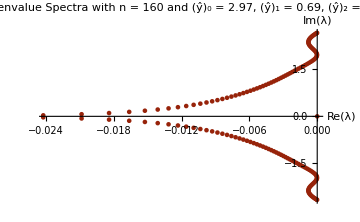
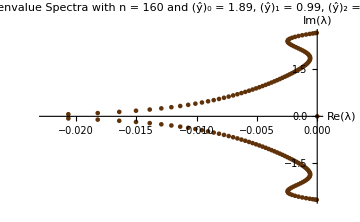
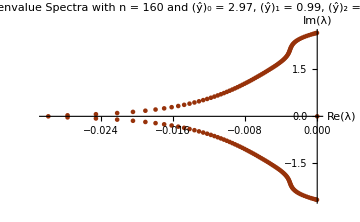
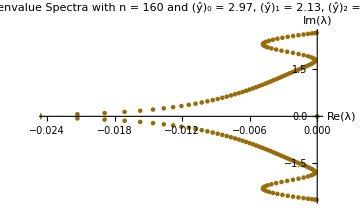
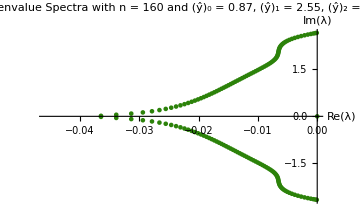
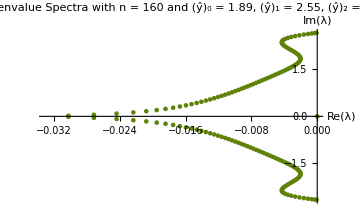
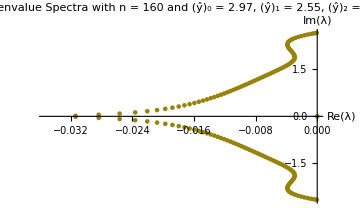
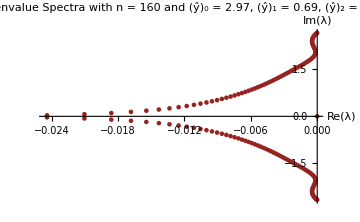

```mathematica
stableplotlist
```

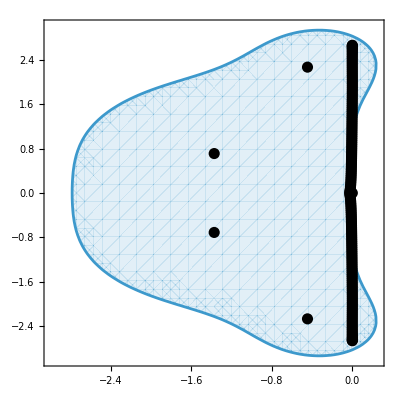
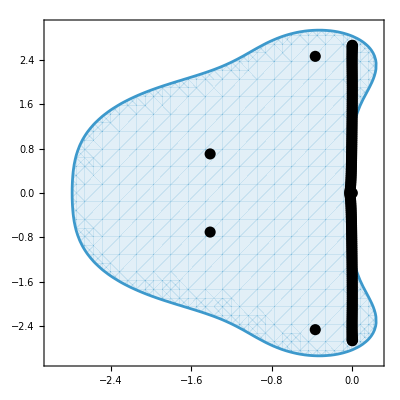
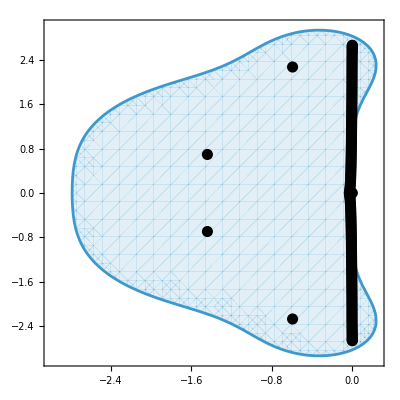
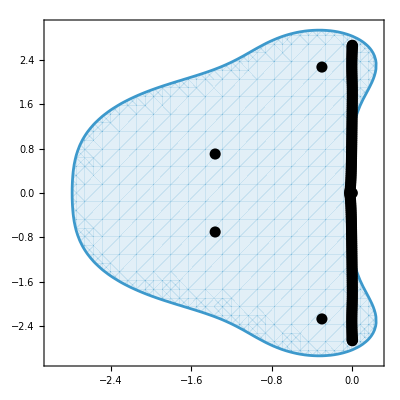
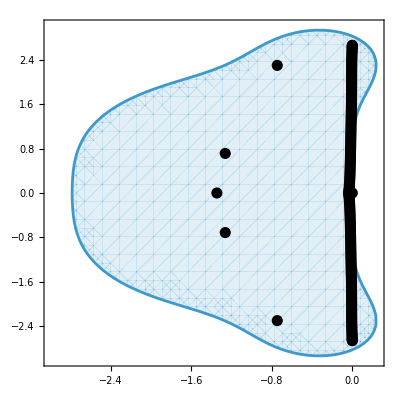
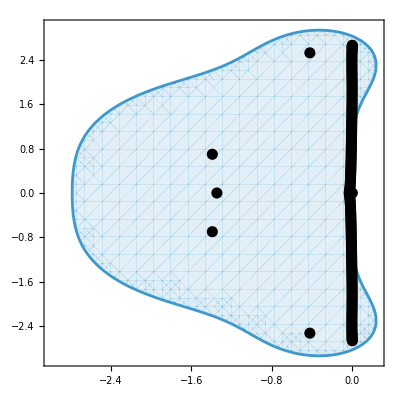
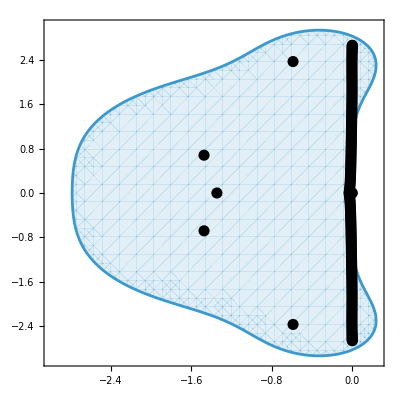
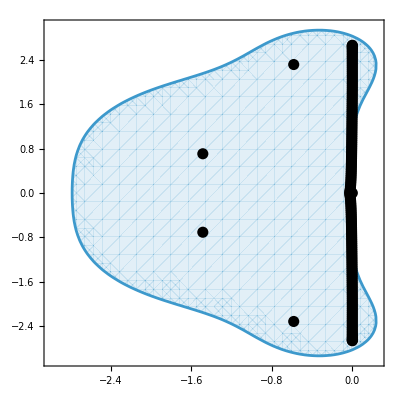
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
stableplotlist2
```

## Max(Re) Fixed

```mathematica
Clear[α,β,a1,a2,a3,yHat2,yHat1,yHat0,yHat]
Clear[γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];



yHat2List={(*1*)0.2,(*2*)0.63,(*3*)1.05,(*4*)1.14,(*5*)1.62,(*6*)2.25,(*7*)2.73,(*8*)3.39,(*9*)3.93,(*10*)4.38,(*11*)4.80};
yHat1List={(*1*)0.69,(*2*)0.99,(*3*)1.65,(*4*)1.95,(*5*)2.13,(*6*)2.55,(*7*)3.06,(*8*)3.12,(*9*)3.42,(*10*)4.23,(*11*)4.35};
yHat0List={(*1*)0.87,(*2*)1.89,(*3*)2.97,(*4*)4.17,(*5*)4.26};

k=160;
Clear[xx,yy,zz]
```

### Parallelization

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\natha\Documents\School\Research\Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks

```mathematica
$ProcessorCount
(*I believe these dump files allow this to now be standalone as long as you setdirectory and don't delete the files*)
(*
DumpSave["bdCoeffs0.mx","Global`bdCoeffs0"]
DumpSave["bdCoeffs1.mx","Global`bdCoeffs1"]
DumpSave["bdCoeffs2.mx","Global`bdCoeffs2"]
DumpSave["interiorCoeffs.mx","Global`interiorCoeffs"]
*)
```

10

```mathematica
LaunchKernels[5]
```

{Local (5),Local (5),Local (5),Local (5),Local (5)}

```mathematica
ParallelEvaluate[Directory[]]
```

{C:\Users\natha\Documents\School\Research\Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\natha\Documents\School\Research\Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\natha\Documents\School\Research\Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\natha\Documents\School\Research\Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\natha\Documents\School\Research\Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks}

```mathematica
ParallelEvaluate[Get["bdCoeffs0.mx"]]
ParallelEvaluate[Get["bdCoeffs1.mx"]]
ParallelEvaluate[Get["bdCoeffs2.mx"]]
ParallelEvaluate[Get["interiorCoeffs.mx"]]
```

{Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null}

«1 more identical outputs»

```mathematica
ParallelEvaluate[ValueQ[bdCoeffs0]]
```

{True,True,True,True,True}

```mathematica
ParallelEvaluate[ByteCount[bdCoeffs0]/2.^30]
```

{1.96897,1.96897,1.96897,1.96897,1.96897}

```mathematica
DistributeDefinitions[(*interiorCoeffs,bdCoeffs1,bdCoeffs2,*)yHat0List,yHat1List,yHat2List,LHS,RHS,LHSRows,RHSRows,k]
```

{yHat0List,yHat1List,yHat2List,LHS,LHSRows,RHS,RHSRows,k}

### Big block of code

```mathematica
maxrelist=ParallelTable[
Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];

γ22val=γ22/.{bdCoeffs2[[3]]/.interiorCoeffs};
γ20val=1/γ22val*(γ20/.{bdCoeffs2[[1]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ21val=1/γ22val*(γ21/.{bdCoeffs2[[2]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ23val=1/γ22val*(γ23/.{bdCoeffs2[[4]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ24val=1/γ22val*(γ24/.{bdCoeffs2[[5]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a20val=1/γ22val*(a20/.{bdCoeffs2[[6]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a21val=1/γ22val*(a21/.{bdCoeffs2[[7]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a22val=1/γ22val*(a22/.{bdCoeffs2[[8]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a23val=1/γ22val*(a23/.{bdCoeffs2[[9]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a24val=1/γ22val*(a24/.{bdCoeffs2[[10]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a25val=1/γ22val*(a25/.{bdCoeffs2[[11]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a26val=1/γ22val*(a26/.{bdCoeffs2[[12]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ22val=γ22val/γ22val/.{yHat->yHat2List[[xx]]};



γ11val=γ11/.{bdCoeffs1[[2]]/.interiorCoeffs};
γ10val=1/γ11val*(γ10/.{bdCoeffs1[[1]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
γ12val=1/γ11val*(γ12/.{bdCoeffs1[[3]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
γ13val=1/γ11val*(γ13/.{bdCoeffs1[[4]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a10val=1/γ11val*(a10/.{bdCoeffs1[[5]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a11val=1/γ11val*(a11/.{bdCoeffs1[[6]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a12val=1/γ11val*(a12/.{bdCoeffs1[[7]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a13val=1/γ11val*(a13/.{bdCoeffs1[[8]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a14val=1/γ11val*(a14/.{bdCoeffs1[[9]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a15val=1/γ11val*(a15/.{bdCoeffs1[[10]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a16val=1/γ11val*(a16/.{bdCoeffs1[[11]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
γ11val=γ11val/γ11val/.{yHat->yHat1List[[yy]]};



γ00val=γ00/.{bdCoeffs0[[1]]/.interiorCoeffs};
γ01val=1/γ00val*(γ01/.{bdCoeffs0[[2]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
γ02val=1/γ00val*(γ02/.{bdCoeffs0[[3]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a00val=1/γ00val*(a00/.{bdCoeffs0[[4]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a01val=1/γ00val*(a01/.{bdCoeffs0[[5]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a02val=1/γ00val*(a02/.{bdCoeffs0[[6]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a03val=1/γ00val*(a03/.{bdCoeffs0[[7]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a04val=1/γ00val*(a04/.{bdCoeffs0[[8]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a05val=1/γ00val*(a05/.{bdCoeffs0[[9]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a06val=1/γ00val*(a06/.{bdCoeffs0[[10]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
γ00val=γ00val/γ00val/.{yHat->yHat0List[[zz]]};


interior={α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392};
boundary={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeff=Flatten[Join[interior,boundary]];



LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeff),
γ13Bar->(γ13/(1-γ10*γ01)/.coeff),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeff),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeff),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeff)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.coeff;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.coeff;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];


LHSNum=(LHS[k]/.coeff)/.barCoeffs;
RHSNum=(RHS[k]/.coeff)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];
{{yHat0List[[zz]],yHat1List[[yy]],yHat2List[[xx]]},Max[Re[eigs]]},
{xx,1,2},{yy,1,2},{zz,1,5}];
```

Kernel 1 working on {1,1,1}

Kernel 2 working on {1,1,2}

Kernel 3 working on {1,1,3}

Kernel 4 working on {1,1,4}

Kernel 5 working on {1,1,5}

Kernel 1 working on {1,2,1}

Kernel 2 working on {1,2,2}

Kernel 3 working on {1,2,3}

Kernel 5 working on {1,2,4}

Kernel 4 working on {1,2,5}

Kernel 1 working on {2,1,1}

Kernel 5 working on {2,1,2}

Kernel 3 working on {2,1,3}

Kernel 2 working on {2,1,4}

Kernel 4 working on {2,1,5}

Kernel 1 working on {2,2,1}

Kernel 3 working on {2,2,2}

Kernel 5 working on {2,2,3}

Kernel 2 working on {2,2,4}

Kernel 4 working on {2,2,5}

```mathematica
maxrelist//TableForm
Dimensions@maxrelist
trimmed=Flatten[maxrelist,2];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]<=0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

0.87
0.69
0.2 | 0.00370991
1.89
0.69
0.2 | 0.0111186
2.97
0.69
0.2 | 0.147291
4.17
0.69
0.2 | 0.493196
4.26
0.69
0.2 | 3.97985 | 0.87
0.99
0.2 | 0.00217669
1.89
0.99
0.2 | 0.00742813
2.97
0.99
0.2 | 0.206115
4.17
0.99
0.2 | 0.39163
4.26
0.99
0.2 | 0.290873
0.87
0.69
0.63 | 0.00528961
1.89
0.69
0.63 | 0.0104879
2.97
0.69
0.63 | 0.217047
4.17
0.69
0.63 | 2.05803
4.26
0.69
0.63 | 6.35375 | 0.87
0.99
0.63 | 0.00135212
1.89
0.99
0.63 | 0.00883387
2.97
0.99
0.63 | 0.328872
4.17
0.99
0.63 | 10.0068
4.26
0.99
0.63 | 4.18859

{2,2,5,2}

{}

0

```mathematica
Clear[α,β,a1,a2,a3,yHat2,yHat1,yHat0,yHat]
Clear[γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

rk4StabilityRegion=RegionPlot[(Abs[1+(x+I y)+(x+I y)^2/2+(x+I y)^3/6+(x+I y)^4/24])<1,{x,-3,0.25},{y,-3,3},PlotStyle->Directive[Opacity[0.15]]];
stableplotlist={};
stableplotlist2={};

For[m=1,m<=Length@stable,m++,
γ22val=γ22val/.{bdCoeffs2[[3]]/.interiorCoeffs};
γ20val=1/γ22val*(γ20/.{bdCoeffs2[[1]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ21val=1/γ22val*(γ21/.{bdCoeffs2[[2]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ23val=1/γ22val*(γ23/.{bdCoeffs2[[4]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ24val=1/γ22val*(γ24/.{bdCoeffs2[[5]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a20val=1/γ22val*(a20/.{bdCoeffs2[[6]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a21val=1/γ22val*(a21/.{bdCoeffs2[[7]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a22val=1/γ22val*(a22/.{bdCoeffs2[[8]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a23val=1/γ22val*(a23/.{bdCoeffs2[[9]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a24val=1/γ22val*(a24/.{bdCoeffs2[[10]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a25val=1/γ22val*(a25/.{bdCoeffs2[[11]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a26val=1/γ22val*(a26/.{bdCoeffs2[[12]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ22val=γ22val/γ22val/.{yHat->yHat2List[[xx]]};



γ11val=γ11val/.{bdCoeffs1[[2]]/.interiorCoeffs};
γ10val=1/γ11val*(γ10/.{bdCoeffs1[[1]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
γ12val=1/γ11val*(γ12/.{bdCoeffs1[[3]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
γ13val=1/γ11val*(γ13/.{bdCoeffs1[[4]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a10val=1/γ11val*(a10/.{bdCoeffs1[[5]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a11val=1/γ11val*(a11/.{bdCoeffs1[[6]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a12val=1/γ11val*(a12/.{bdCoeffs1[[7]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a13val=1/γ11val*(a13/.{bdCoeffs1[[8]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a14val=1/γ11val*(a14/.{bdCoeffs1[[9]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a15val=1/γ11val*(a15/.{bdCoeffs1[[10]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a16val=1/γ11val*(a16/.{bdCoeffs1[[11]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
γ11val=γ11val/γ11val/.{yHat->yHat1List[[yy]]};



γ00val=γ00val/.{bdCoeffs0[[1]]/.interiorCoeffs};
γ01val=1/γ00val*(γ01/.{bdCoeffs0[[2]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
γ02val=1/γ00val*(γ02/.{bdCoeffs0[[3]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a00val=1/γ00val*(a00/.{bdCoeffs0[[4]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a01val=1/γ00val*(a01/.{bdCoeffs0[[5]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a02val=1/γ00val*(a02/.{bdCoeffs0[[6]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a03val=1/γ00val*(a03/.{bdCoeffs0[[7]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a04val=1/γ00val*(a04/.{bdCoeffs0[[8]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a05val=1/γ00val*(a05/.{bdCoeffs0[[9]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a06val=1/γ00val*(a06/.{bdCoeffs0[[10]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
γ00val=γ00val/γ00val/.{yHat->yHat0List[[zz]]};

interior={α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392};
boundary={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeff=Flatten[Join[interior,boundary]];



{γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeff),
γ13Bar->(γ13/(1-γ10*γ01)/.coeff),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeff),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeff),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeff)};

Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.coeff;
Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.coeff;

barCoeffs=Join[%,%%,%%%];
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];


LHSNum=(LHS[k]/.coeff)/.barCoeffs;
RHSNum=(RHS[k]/.coeff)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

AppendTo[stableplotlist,
ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[160]," and\n","(ŷ)_0 = ",ToString[stable[[m,1,1]]],", (ŷ)_1 = ",ToString[stable[[m,1,2]]],", (ŷ)_2 = ",ToString[stable[[m,1,3]]]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[stable[[m,1,1]]/5,stable[[m,1,2]]/5,stable[[m,1,3]]/5]]];
AppendTo[stableplotlist2,
Show[rk4StabilityRegion,ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[160]," and\n","(ŷ)_0 = ",ToString[stable[[m,1,1]]],", (ŷ)_1 = ",ToString[stable[[m,1,2]]],", (ŷ)_2 = ",ToString[stable[[m,1,3]]]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->{RGBColor[0,0,0],PointSize[0.02]}]]]
];
```

```mathematica
stableplotlist
```

```mathematica
stableplotlist2
```